```mathematica
A={{2,-1},{-1,1}};(*{{2,-1},{-0.5,1}};*)
b={1,1};
```

```mathematica
A//MatrixForm
```

(2 | -1
0.2 | 1)

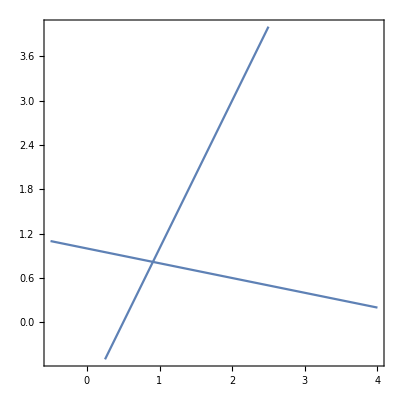

```mathematica
gr=ContourPlot[A.{x,y}==b,{x,-0.5,4},{y,-0.5,4},Axes->True]
```

```mathematica
d=IdentityMatrix[2]*A;
```

```mathematica
d//MatrixForm
```

(2 | 0
0. | 1)

```mathematica
l={{0,0},{1,0}}*A;
```

```mathematica
l//MatrixForm
```

(0 | 0
-1 | 0)

```mathematica
u={{0,1},{0,0}}*A;
```

```mathematica
u//MatrixForm
```

(0 | -1
0 | 0)

```mathematica
ω=1;
```

```mathematica
c=-Inverse[d/ω-l].(u+(ω-1)/ω d);
```

```mathematica
c//MatrixForm
```

(0. | 0.5
0. | 0.1)

```mathematica
xt=LinearSolve[A,b]//N;
```

```mathematica
Norm[c,∞]
```

0.5

```mathematica
(*b1=Inverse[d/ω-l].b;*)
```

```mathematica
(*j=1;*)
```

```mathematica
(*xpr={{0,0}};*)
```

```mathematica
(*While[Norm[xpr[[j]]-xt]>0.0001,xpr=Append[xpr,c.xpr[[j]]+b1];j++];*)
```

```mathematica
(*j*)
```

```mathematica
xpr={{0,0}};
```

```mathematica
x1=xpr[[1]][[1]];
x2=xpr[[1]][[2]];
k=0;
```

```mathematica
While[Norm[xpr[[-1]]-xt]>0.0001,x1=(1-ω)x1-ω (A[[1]][[2]])/(A[[1]][[1]]) x2+ω b[[1]]/(A[[1]][[1]]);xpr=Append[xpr,{x1,x2}];
x2=(1-ω)x2-ω(A[[2]][[1]])/(A[[2]][[2]])x1+ω b[[2]]/(A[[2]][[2]]);xpr=Append[xpr,{x1,x2}];k++];
```

```mathematica
k
```

5

```mathematica
(*МЕТОД ЗЕЙДЕЛЯ*)
```

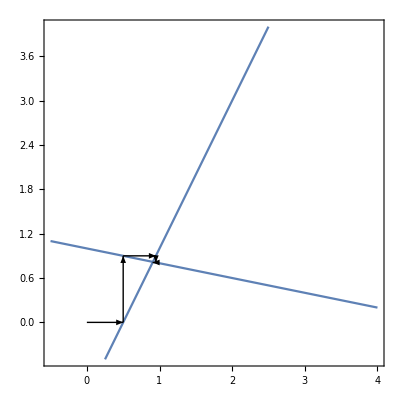

```mathematica
Show[gr,Graphics[{Arrowheads[0.015],Table[Arrow[{xpr[[i]],xpr[[i+1]]}],{i,1,k}]}]]
```

```mathematica
(*МЕТОД РЕЛАКСАЦИИ*)
```

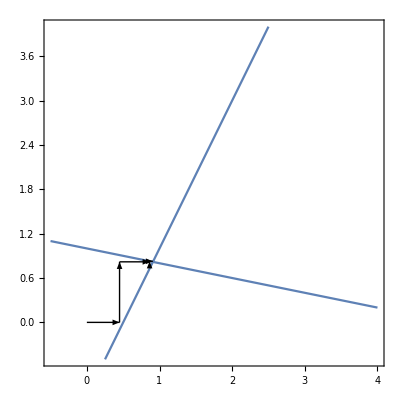

```mathematica
Show[gr,Graphics[{Arrowheads[0.015],Table[Arrow[{xpr[[i]],xpr[[i+1]]}],{i,1,k}]}]]
```

```mathematica
(*МЕТОД ЗЕЙДЕЛЯ*)
```

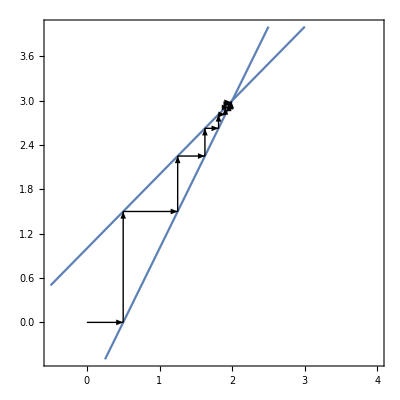

```mathematica
Show[gr,Graphics[{Arrowheads[0.015],Table[Arrow[{xpr[[i]],xpr[[i+1]]}],{i,1,k}]}]]
```

```mathematica
(*МЕТОД РЕЛАКСАЦИИ*)
```

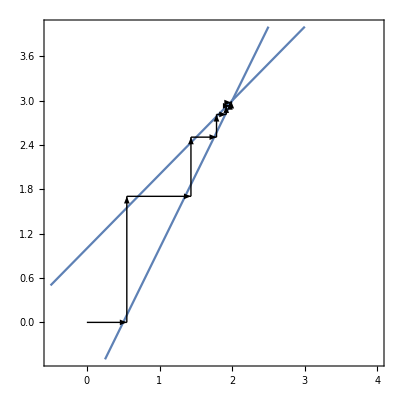

```mathematica
Show[gr,Graphics[{Arrowheads[0.015],Table[Arrow[{xpr[[i]],xpr[[i+1]]}],{i,1,k}]}]]
```